# Método de los momentos dividiendo el dominio - Chi cuadrado 5 g.l.

```mathematica
(*Muestra de la distribución Chi Cuadrado con 5 g.l.*)
```

```mathematica
SeedRandom[1234]
```

```mathematica
datos2 = RandomVariate[ChiSquareDistribution[5],10^4]
```

{4.76251,1.52784,4.3168,3.1357,7.60988,6.72557,9988,2.77825,2.44833,10.6619,9.3595,1.46811,2.68483}
 |  |  |  |

```mathematica
datos=ReplacePart[datos2,{2514-> 9.170447257086153,4287-> 3.008506020714771,8676-> 4.6168058605179905}]
```

{4.76251,1.52784,4.3168,3.1357,7.60988,6.72557,9988,2.77825,2.44833,10.6619,9.3595,1.46811,2.68483}
 |  |  |  |

### MOP DE GRADO 2

```mathematica
F2[x_]=Piecewise[{{b*x+c*x^2,0≤x<3},{d+e*x+f*x^2,3≤x<Infinity}},0]
```

Piecewise[{{b x+c x^2, 0≤x<3}, {d+e x+f x^2, 3≤x<∞}, {0, True}}]

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*F2[x],{x,0,25}]
```

1/12 (108 b+243 c+3696 d+62392 e+1171632 f)

```mathematica
Integrate[x^2*F2[x],{x,0,25}]
```

1/60 (1215 b+2916 c+311960 d+5858160 e+117184584 f)

```mathematica
Integrate[x^3*F2[x],{x,0,25}]
```

1/30 (1458 b+3645 c+2929080 d+58592292 e+1220699480 f)

```mathematica
Integrate[x^4*F2[x],{x,0,25}]
```

1/210 (25515 b+65610 c+410146044 d+8544896360 e+183105403140 f)

```mathematica
Integrate[x^5*F2[x],{x,0,25}]
```

1/168 (52488 b+137781 c+6835917088 d+146484322512 e+3204345565344 f)

```mathematica
(*Solución matricial del sistema*)
```

```mathematica
{{Integrate[x*F2[x],{x,0,25}]},{Integrate[x^2*F2[x],{x,0,25}]},{Integrate[x^3*F2[x],{x,0,25}]},{Integrate[x^4*F2[x],{x,0,25}]},{Integrate[x^5*F2[x],{x,0,25}]}}
```

```mathematica
M2={{1/12 108,1/12 243 ,1/12 3696 ,1/12 62392 ,1/12 1171632 },{1/60 1215 ,1/60 2916 ,1/60 311960 ,1/60 5858160 ,1/60 117184584 },{1/30 1458,1/30 3645 ,1/30 2929080 ,1/30 58592292 ,1/30 1220699480 },{1/210 25515 ,1/210 65610 ,1/210 410146044 ,1/210 8544896360 ,1/210 183105403140 },{1/168 52488 ,1/168 137781 ,1/168 6835917088 ,1/168 146484322512 ,1/168 3204345565344 }}
```

{{9,81/4,308,15598/3,97636},{81/4,243/5,15598/3,97636,9765382/5},{243/5,243/2,97636,9765382/5,122069948/3},{243/2,2187/7,9765382/5,122069948/3,6103513438/7},{2187/7,6561/8,122069948/3,6103513438/7,19073485508}}

```mathematica
MatrixForm[M2]
```

(9 | 81/4 | 308 | 15598/3 | 97636
81/4 | 243/5 | 15598/3 | 97636 | 9765382/5
243/5 | 243/2 | 97636 | 9765382/5 | 122069948/3
243/2 | 2187/7 | 9765382/5 | 122069948/3 | 6103513438/7
2187/7 | 6561/8 | 122069948/3 | 6103513438/7 | 19073485508)

```mathematica
B2={{(Apply[Plus,datos])/(10^4)},{(Apply[Plus,datos^2])/(10^4)},{(Apply[Plus,datos^3])/(10^4)},{(Apply[Plus,datos^4])/(10^4)},{(Apply[Plus,datos^5])/(10^4)}}
```

{{5.06637},{35.7888},{322.891},{3521.88},{44666.}}

```mathematica
Sol2=Inverse[M2].B2
```

{{-0.826644},{0.436114},{0.124937},{-0.0122434},{0.000295501}}

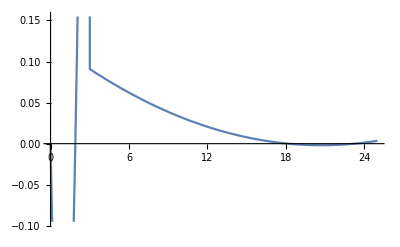

```mathematica
Plot[F2[x]/.{b->-0.8266437942276958,c->0.4361135427622571,d->0.12493714184609228,e->-0.012243367573123554,f->0.00029550141718364775},{x,0,25}]
```

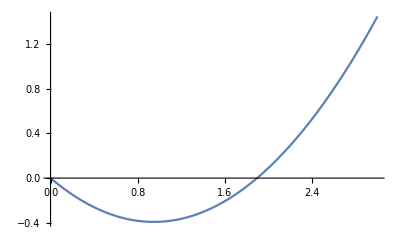

```mathematica
Plot[F2[x]/.{b->-0.8266437942276958,c->0.4361135427622571,d->0.12493714184609228,e->-0.012243367573123554,f->0.00029550141718364775},{x,0,3}]
```

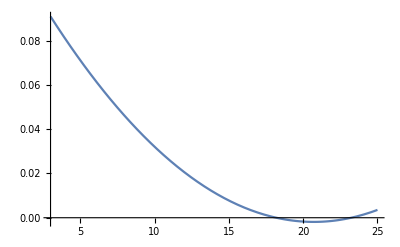

```mathematica
Plot[F2[x]/.{b->-0.8266437942276958,c->0.4361135427622571,d->0.12493714184609228,e->-0.012243367573123554,f->0.00029550141718364775},{x,3,25}]
```

### MOP DE GRADO 3

```mathematica
F3[x_]=Piecewise[{{b*x+c*x^2+d*x^3,0≤x<3},{e+f*x+g*x^2+h*x^3,3≤x<Infinity}},0]
```

Piecewise[{{b x+c x^2+d x^3, 0≤x<3}, {e+f x+g x^2+h x^3, 3≤x<∞}, {0, True}}]

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*F3[x],{x,0,25}]
```

1/60 (540 b+1215 c+2916 d+18480 e+311960 f+5858160 g+117184584 h)

```mathematica
Integrate[x^2*F3[x],{x,0,25}]
```

1/60 (1215 b+2916 c+7290 d+311960 e+5858160 f+117184584 g+2441398960 h)

```mathematica
Integrate[x^3*F3[x],{x,0,25}]
```

1/210 (10206 b+25515 c+65610 d+20503560 e+410146044 f+8544896360 g+183105403140 h)

```mathematica
Integrate[x^4*F3[x],{x,0,25}]
```

1/840 (102060 b+262440 c+688905 d+1640584176 e+34179585440 f+732421612560 g+16021727826720 h)

```mathematica
Integrate[x^5*F3[x],{x,0,25}]
```

1/504 (157464 b+413343 c+1102248 d+20507751264 e+439452967536 f+9613036696032 g+213623045772752 h)

```mathematica
Integrate[x^6*F3[x],{x,0,25}]
```

1/2520(2066715 b+5511240 c+14880348 d+2197264837680 e+48065183480160 f+1068115228863760 g+24032592758557152 h)

```mathematica
Integrate[x^7*F3[x],{x,0,25}]
```

1/990 (2165130 b+5845851 c+15943230 d+18882750652920 e+419616697053620 f+9441375726576024 g+214576721175463020 h)

```mathematica
(*Solución del sistema*)
```

```mathematica
Solve[{1/60 (540 b+1215 c+2916 d+18480 e+311960 f+5858160 g+117184584 h)==(Apply[Plus,datos])/(10^4),1/60 (1215 b+2916 c+7290 d+311960 e+5858160 f+117184584 g+2441398960 h)==(Apply[Plus,datos^2])/(10^4),1/210 (10206 b+25515 c+65610 d+20503560 e+410146044 f+8544896360 g+183105403140 h)==(Apply[Plus,datos^3])/(10^4),1/840 (102060 b+262440 c+688905 d+1640584176 e+34179585440 f+732421612560 g+16021727826720 h)==(Apply[Plus,datos^4])/(10^4),1/504 (157464 b+413343 c+1102248 d+20507751264 e+439452967536 f+9613036696032 g+213623045772752 h)==(Apply[Plus,datos^5])/(10^4),1/2520(2066715 b+5511240 c+14880348 d+2197264837680 e+48065183480160 f+1068115228863760 g+24032592758557152 h)==(Apply[Plus,datos^6])/(10^4),1/990 (2165130 b+5845851 c+15943230 d+18882750652920 e+419616697053620 f+9441375726576024 g+214576721175463020 h)==(Apply[Plus,datos^7])/(10^4)},{b,c,d,e,f,g,h}]
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{1.95308×10^6,97636.,5199.33,308.,48.6,20.25,9.,-5.07256},{4.069×10^7,1.95308×10^6,97636.,5199.33,121.5,48.6,20.25,-35.984},{8.7193×10^8,4.069×10^7,1.95308×10^6,97636.,312.429,121.5,48.6,-328.226},{«1»},{«22»,«6»,-«18»},{9.53674×10^12,4.23855×10^11,1.90735×10^10,8.7193×10^8,5904.9,2187.,820.125,-737352.},{2.16744×10^14,9.53674×10^12,4.23855×10^11,1.90735×10^10,16104.3,5904.9,2187.,-1.26495×10^7}} may contain significant numerical errors.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→-0.30436-1.11246 b,d→0.145341+0.278685 b,e→0.22607-0.0018023 b,f→-0.032439+0.000314548 b,g→0.00154255-0.000017558 b,h→-0.0000242717+3.16039×10^-7 b}}

```mathematica
(*Solución matricial del sistema*)
```

```mathematica
M3 = {{1/60 540 ,1/60 1215 ,1/60 2916 ,1/60 18480 ,1/60 311960 ,1/60 5858160 ,1/60 117184584 },{1/60 1215 ,1/60 2916 ,1/60 7290 ,1/60 311960 ,1/60 5858160 ,1/60 117184584 ,1/60 2441398960 },{1/210 10206 ,1/210 25515 ,1/210 65610 ,1/210 20503560 ,1/210 410146044 ,1/210 8544896360 ,1/210 183105403140 },{1/840 102060 ,1/840 262440 ,1/840 688905 ,1/840 1640584176 ,1/840 34179585440 ,1/840 732421612560 ,1/840 16021727826720 },{1/504 157464 ,1/504 413343 ,1/504 1102248 ,1/504 20507751264 ,1/504 439452967536 ,1/504 9613036696032 ,1/504 213623045772752 },{1/2520 2066715 ,1/2520 5511240 ,1/2520 14880348 ,1/2520 2197264837680 ,1/2520 48065183480160 ,1/2520 1068115228863760 ,1/2520 24032592758557152 },{1/990 2165130 ,1/990 5845851 ,1/990 15943230 ,1/990 18882750652920 ,1/990 419616697053620 ,1/990 9441375726576024 ,1/990 214576721175463020 }}
```

{{9,81/4,243/5,308,15598/3,97636,9765382/5},{81/4,243/5,243/2,15598/3,97636,9765382/5,122069948/3},{243/5,243/2,2187/7,97636,9765382/5,122069948/3,6103513438/7},{243/2,2187/7,6561/8,9765382/5,122069948/3,6103513438/7,19073485508},{2187/7,6561/8,2187,122069948/3,6103513438/7,19073485508,3814697245942/9},{6561/8,2187,59049/10,6103513438/7,19073485508,3814697245942/9,47683715790788/5},{2187,59049/10,177147/11,19073485508,3814697245942/9,47683715790788/5,216744162803498}}

```mathematica
MatrixForm[M3]
```

(9 | 81/4 | 243/5 | 308 | 15598/3 | 97636 | 9765382/5
81/4 | 243/5 | 243/2 | 15598/3 | 97636 | 9765382/5 | 122069948/3
243/5 | 243/2 | 2187/7 | 97636 | 9765382/5 | 122069948/3 | 6103513438/7
243/2 | 2187/7 | 6561/8 | 9765382/5 | 122069948/3 | 6103513438/7 | 19073485508
2187/7 | 6561/8 | 2187 | 122069948/3 | 6103513438/7 | 19073485508 | 3814697245942/9
6561/8 | 2187 | 59049/10 | 6103513438/7 | 19073485508 | 3814697245942/9 | 47683715790788/5
2187 | 59049/10 | 177147/11 | 19073485508 | 3814697245942/9 | 47683715790788/5 | 216744162803498)

```mathematica
MatrixRank[M3]
```

7

```mathematica
B3 = {(Apply[Plus,datos])/(10^4),(Apply[Plus,datos^2])/(10^4),(Apply[Plus,datos^3])/(10^4),(Apply[Plus,datos^4])/(10^4),(Apply[Plus,datos^5])/(10^4),(Apply[Plus,datos^6])/(10^4),(Apply[Plus,datos^7])/(10^4)}
```

{5.06637,35.7888,322.891,3521.88,44666.,638998.,1.00622×10^7}

```mathematica
Sol3 = Inverse[M3].B3
```

{2.75599,-3.26165,0.866282,0.237321,-0.0348115,0.00169666,-0.0000274148}

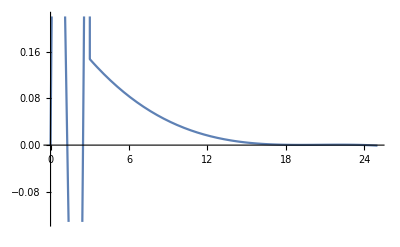

```mathematica
Plot[F3[x]/.{b->2.7559880580902245,c->-3.2616518030396264,d->0.8662824095304416,e->0.23732110873851298,f->-0.034811545643098185,g->0.0016966562516839145,h->-0.000027414799663693246},{x,0,25}]
```

```mathematica
F3[x]/.{b->2.7559880580902245,c->-3.2616518030396264,d->0.8662824095304416,e->0.23732110873851298,f->-0.034811545643098185,g->0.0016966562516839145,h->-0.000027414799663693246}
```

Piecewise[{{2.75599 x-3.26165 x^2+0.866282 x^3, 0≤x<3}, {0.237321-0.0348115 x+0.00169666 x^2-0.0000274148 x^3, 3≤x<∞}, {0, True}}]

```mathematica
F31[x_]= 2.7559880580902245 x-3.2616518030396264 x^2+0.8662824095304416 x^3
```

2.75599 x-3.26165 x^2+0.866282 x^3

```mathematica
F32[x_]=0.23732110873851298-0.034811545643098185 x+0.0016966562516839145 x^2-0.000027414799663693246 x^3
```

0.237321-0.0348115 x+0.00169666 x^2-0.0000274148 x^3

```mathematica
Solve[F31[x]==0,Reals]
```

{{x→0},{x→1.28037},{x→2.48474}}

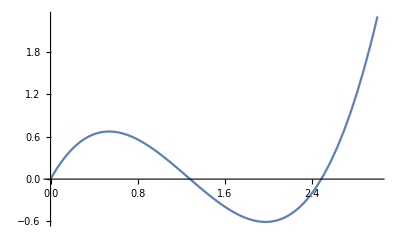

```mathematica
Plot[F31[x],{x,0,3}]
```

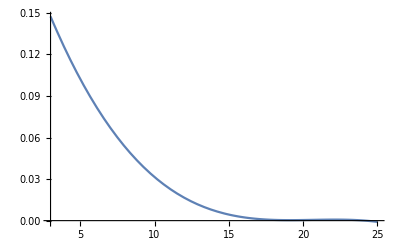

```mathematica
Plot[F32[x],{x,3,25}]
```

```mathematica
FindMinimum[F31[x],{x,2}]
```

{-0.605807,{x→1.97243}}

```mathematica
F31[x]+0.6058068804209364
```

0.605807+2.75599 x-3.26165 x^2+0.866282 x^3

```mathematica
Solve[F32[x]==0,Reals]
```

{{x→24.1713}}

```mathematica
F32[25]
```

-0.00091362

```mathematica
F33[x_]= Piecewise[{{F31[x]+0.6058068804209364,0≤x<3},{F32[x]+0.0009136197817019021,3≤x≤Infinity}},0]
```

Piecewise[{{0.605807+2.75599 x-3.26165 x^2+0.866282 x^3, 0≤x<3}, {0.238235-0.0348115 x+0.00169666 x^2-0.0000274148 x^3, 3≤x≤∞}, {0, True}}]

```mathematica
Integrate[F33[x],{x,0,25}]
```

3.07074

```mathematica
f3[x_]=Piecewise[{{(0.6058068804209364+2.7559880580902245 x-3.2616518030396264 x^2+0.8662824095304416 x^3)/3.070737462298324,0≤x<3},{(0.23823472852021488-0.034811545643098185 x+0.0016966562516839145 x^2-0.000027414799663693246 x^3)/3.070737462298324,3≤x≤Infinity}},0]
```

Piecewise[{{0.325655 (0.605807+2.75599 x-3.26165 x^2+0.866282 x^3), 0≤x<3}, {0.325655 (0.238235-0.0348115 x+0.00169666 x^2-0.0000274148 x^3), 3≤x≤∞}, {0, True}}]

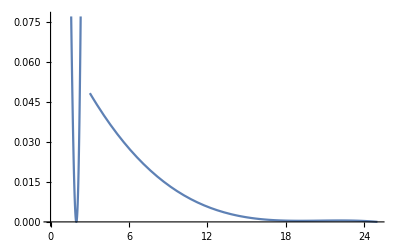

```mathematica
Plot[f3[x],{x,0,25}]
```

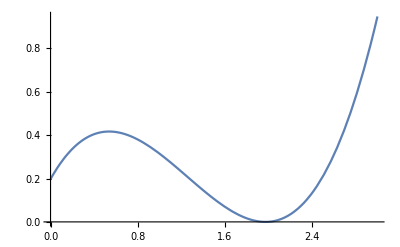

```mathematica
Plot[f3[x],{x,0,3}]
```

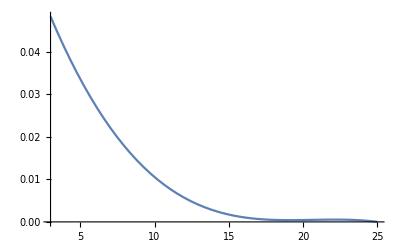

```mathematica
Plot[f3[x],{x,3,25}]
```

```mathematica
(*Divergencia de Kullback-Leibler*)
```

```mathematica
N[Integrate[PDF[ChiSquareDistribution[5],x],{x,0,25}]]
```

0.999861

```mathematica
G[x_]= (PDF[ChiSquareDistribution[5],x])/0.9998606662088144
```

1.00014 (Piecewise[{{(ⅇ^(-x/2) x^(3/2))/(3 √(2 π)), x>0}, {0, True}}])

```mathematica
KL3=N[Integrate[G[x]*Log[G[x]/f3[x]],{x,0,25}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.97456}. NIntegrate obtained 0.89089 and 0.00062226 for the integral and error estimates.

0.89089

```mathematica
F4[x_] = Piecewise[{{b*x+c*x^2+d*x^3+e*x^4,0≤x<3},{f+g*x+h*x^2+i*x^3+j*x^4,3≤x<Infinity}},0]
```

Piecewise[{{b x+c x^2+d x^3+e x^4, 0≤x<3}, {f+g x+h x^2+i x^3+j x^4, 3≤x<∞}, {0, True}}]

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*F4[x],{x,0,25}]
```

1/60 (540 b+1215 c+2916 d+7290 e+18480 f+311960 g+5858160 h+117184584 i+2441398960 j)

```mathematica
Integrate[x^2*F4[x],{x,0,25}]
```

1/420 (8505 b+20412 c+51030 d+131220 e+2183720 f+41007120 g+820292088 h+17089792720 i+366210806280 j)

```mathematica
Integrate[x^3*F4[x],{x,0,25}]
```

1/840 (40824 b+102060 c+262440 d+688905 e+82014240 f+1640584176 g+34179585440 h+732421612560 i+16021727826720 j)

```mathematica
Integrate[x^4*F4[x],{x,0,25}]
```

1/2520(306180 b+787320 c+2066715 d+5511240 e+4921752528 f+102538756320 g+2197264837680 h+48065183480160 i+1068115228863760 j)

```mathematica
Integrate[x^5*F4[x],{x,0,25}]
```

1/2520(787320 b+2066715 c+5511240 d+14880348 e+102538756320 f+2197264837680 g+48065183480160 h+1068115228863760 i+24032592758557152 j)

```mathematica
Integrate[x^6*F4[x],{x,0,25}]
```

1/27720(22733865 b+60623640 c+163683828 d+446410440 e+24169913214480 f+528717018281760 g+11749267517501360 h+264358520344128672 i+6008148192912964560 j)

```mathematica
Integrate[x^7*F4[x],{x,0,25}]
```

1/1980(4330260 b+11691702 c+31886460 d+87687765 e+37765501305840 f+839233394107240 g+18882751453152048 h+429153442350926040 i+9834766387851765360 j)

```mathematica
Integrate[x^8*F4[x],{x,0,25}]
```

1/25740(151992126 b+414523980 c+1139940945 d+3156759540 e+10910034123394120 f+245475768890976624 g+5578994750562038520 h+127851963042072949680 i+2950429916378679177960 j)

```mathematica
Integrate[x^9*F4[x],{x,0,25}]
```

1/60060(967222620 b+2659862205 c+7365772260 d+20518937010 e+572776794078945456 f+13017654417978089880 g+298321247098170215920 h+6884336471550251415240 i+159814953803995594344240 j)

```mathematica
(*Solución matricial del sistema*)
```

```mathematica
M4={}
```

```mathematica
F5[x_] = Piecewise[{{b*x+c*x^2+d*x^3+e*x^4+f*x^5,0≤x<3},{g+h*x+i*x^2+j*x^3+k*x^4+l*x^5,3≤x≤Infinity}},0]
```

Piecewise[{{b x+c x^2+d x^3+e x^4+f x^5, 0≤x<3}, {g+h x+i x^2+j x^3+k x^4+l x^5, 3≤x≤∞}, {0, True}}]

```mathematica
(*Momentos poblacionales*)
```

```mathematica
Integrate[x*F5[x],{x,0,25}]
```

1/420 (3780 b+8505 c+20412 d+51030 e+131220 f+129360 g+2183720 h+41007120 i+820292088 j+17089792720 k+366210806280 l)

```mathematica
Integrate[x^2*F5[x],{x,0,25}]
```

1/840 (17010 b+40824 c+102060 d+262440 e+688905 f+4367440 g+82014240 h+1640584176 i+34179585440 j+732421612560 k+16021727826720 l)

```mathematica
Integrate[x^3*F5[x],{x,0,25}]
```

1/2520(122472 b+306180 c+787320 d+2066715 e+5511240 f+246042720 g+4921752528 h+102538756320 i+2197264837680 j+48065183480160 k+1068115228863760 l)

```mathematica
Integrate[x^4*F5[x],{x,0,25}]
```

1/2520(306180 b+787320 c+2066715 d+5511240 e+14880348 f+4921752528 g+102538756320 h+2197264837680 i+48065183480160 j+1068115228863760 k+24032592758557152 l)

```mathematica
Integrate[x^5*F5[x],{x,0,25}]
```

1/27720(8660520 b+22733865 c+60623640 d+163683828 e+446410440 f+1127926319520 g+24169913214480 h+528717018281760 i+11749267517501360 j+264358520344128672 k+6008148192912964560 l)

```mathematica
Integrate[x^6*F5[x],{x,0,25}]
```

1/27720(22733865 b+60623640 c+163683828 d+446410440 e+1227628710 f+24169913214480 g+528717018281760 h+11749267517501360 i+264358520344128672 j+6008148192912964560 k+137686729429924715040 l)

```mathematica
Integrate[x^7*F5[x],{x,0,25}]
```

1/25740(56293380 b+151992126 c+414523980 d+1139940945 e+3156759540 f+490951516975920 g+10910034123394120 h+245475768890976624 i+5578994750562038520 j+127851963042072949680 k+2950429916378679177960 l)

```mathematica
Integrate[x^8*F5[x],{x,0,25}]
```

1/180180(1063944882 b+2901667860 c+7979586615 d+22097316780 e+61556811030 f+76370238863758840 g+1718330382236836368 h+39052963253934269640 i+894963741294510647760 j+20653009414650754245720 k+479444861411986783032720 l)

```mathematica
Integrate[x^9*F5[x],{x,0,25}]
```

1/60060(967222620 b+2659862205 c+7365772260 d+20518937010 e+57453023628 f+572776794078945456 g+13017654417978089880 h+298321247098170215920 i+6884336471550251415240 j+159814953803995594344240 k+3729015588760318523538872 l)

```mathematica
Integrate[x^10*F5[x],{x,0,25}]
```

1/21840(967222620 b+2678462640 c+7461431640 d+20892008592 e+58758774165 f+4733692515628396320 g+108480453490243714880 h+2503395080563727787360 i+58114528655998397943360 j+1356005668640115826741408 k+31781382858753145586928960 l)

```mathematica
Integrate[x^11*F5[x],{x,0,25}]
```

1/371280(45533864880 b+126844337880 c+355164146064 d+998899160805 e+2820421159920 f+1844167709334143152960 g+42557716369583372385120 h+987946987151972765037120 i+23052096366881969054603936 j+540283508598803474977792320 k+12712553143501278917860090080 l)

```mathematica
(*Solución matricial del sistema*)
```

```mathematica
{{Integrate[x*F5[x],{x,0,25}]},{Integrate[x^2*F5[x],{x,0,25}]},{Integrate[x^3*F5[x],{x,0,25}]},{Integrate[x^4*F5[x],{x,0,25}]},{Integrate[x^5*F5[x],{x,0,25}]},{Integrate[x^6*F5[x],{x,0,25}]},{Integrate[x^7*F5[x],{x,0,25}]},{Integrate[x^8*F5[x],{x,0,25}]},{Integrate[x^9*F5[x],{x,0,25}]},{Integrate[x^10*F5[x],{x,0,25}]},{Integrate[x^11*F5[x],{x,0,25}]}}
```

```mathematica
M5={{ 1/420 3780 ,1/420 8505 ,1/420 20412 ,1/420 51030 ,1/420 131220 ,1/420 129360 ,1/420 2183720 ,1/420 41007120 ,1/420 820292088 ,1/420 17089792720 ,1/420 366210806280 },{ 1/840 17010 ,1/840 40824 ,1/840 102060 ,1/840 262440 ,1/840 688905 ,1/840 4367440 ,1/840 82014240 ,1/840 1640584176 ,1/840 34179585440 ,1/840 732421612560 ,1/840 16021727826720 },{1/2520 122472 ,1/2520 306180 ,1/2520 787320 ,1/2520 2066715 ,1/2520 5511240 ,1/2520 246042720 ,1/2520 4921752528 ,1/2520 102538756320 ,1/2520 2197264837680 ,1/2520 48065183480160 ,1/2520 1068115228863760 },{1/2520 306180 ,1/2520 787320 ,1/2520 2066715 ,1/2520 5511240 ,1/2520 14880348 ,1/2520 4921752528 ,1/2520 102538756320 ,1/2520 2197264837680 ,1/2520 48065183480160 ,1/2520 1068115228863760 ,1/2520 24032592758557152 },{1/27720 8660520 ,1/27720 22733865 ,1/27720 60623640 ,1/27720 163683828 ,1/27720 446410440 ,1/27720 1127926319520 ,1/27720 24169913214480 ,1/27720 528717018281760 ,1/27720 11749267517501360 ,1/27720 264358520344128672 ,1/27720 6008148192912964560 },{1/27720 22733865 ,1/27720 60623640 ,1/27720 163683828 ,1/27720 446410440 ,1/27720 1227628710 ,1/27720 24169913214480 ,1/27720 528717018281760 ,1/27720 11749267517501360 ,1/27720 264358520344128672 ,1/27720 6008148192912964560 ,1/27720 137686729429924715040 },{1/25740 56293380 ,1/25740 151992126 ,1/25740 414523980 ,1/25740 1139940945 ,1/25740 3156759540 ,1/25740 490951516975920 ,1/25740 10910034123394120 ,1/25740 245475768890976624 ,1/25740 5578994750562038520 ,1/25740 127851963042072949680 ,1/25740 2950429916378679177960 },{1/180180 1063944882 ,1/180180 2901667860 ,1/180180 7979586615 ,1/180180 22097316780 ,1/180180 61556811030 ,1/180180 76370238863758840 ,1/180180 1718330382236836368 ,1/180180 39052963253934269640 ,1/180180 894963741294510647760 ,1/180180 20653009414650754245720 ,1/180180 479444861411986783032720 },{1/60060 967222620 ,1/60060 2659862205 ,1/60060 7365772260 ,1/60060 20518937010 ,1/60060 57453023628 ,1/60060 572776794078945456 ,1/60060 13017654417978089880 ,1/60060 298321247098170215920 ,1/60060 6884336471550251415240 ,1/60060 159814953803995594344240 ,1/60060 3729015588760318523538872 },{1/21840 967222620 ,1/21840 2678462640 ,1/21840 7461431640 ,1/21840 20892008592 ,1/21840 58758774165 ,1/21840 4733692515628396320 ,1/21840 108480453490243714880 ,1/21840 2503395080563727787360 ,1/21840 58114528655998397943360 ,1/21840 1356005668640115826741408 ,1/21840 31781382858753145586928960 },{1/371280 45533864880 ,1/371280 126844337880 ,1/371280 355164146064 ,1/371280 998899160805 ,1/371280 2820421159920 ,1/371280 1844167709334143152960 ,1/371280 42557716369583372385120 ,1/371280 987946987151972765037120 ,1/371280 23052096366881969054603936 ,1/371280 540283508598803474977792320 ,1/371280 12712553143501278917860090080 }}
```

{{9,81/4,243/5,243/2,2187/7,308,15598/3,97636,9765382/5,122069948/3,6103513438/7},{81/4,243/5,243/2,2187/7,6561/8,15598/3,97636,9765382/5,122069948/3,6103513438/7,19073485508},{243/5,243/2,2187/7,6561/8,2187,97636,9765382/5,122069948/3,6103513438/7,19073485508,3814697245942/9},{243/2,2187/7,6561/8,2187,59049/10,9765382/5,122069948/3,6103513438/7,19073485508,3814697245942/9,47683715790788/5},{2187/7,6561/8,2187,59049/10,177147/11,122069948/3,6103513438/7,19073485508,3814697245942/9,47683715790788/5,216744162803498},{6561/8,2187,59049/10,177147/11,177147/4,6103513438/7,19073485508,3814697245942/9,47683715790788/5,216744162803498,14901161193714796/3},{2187,59049/10,177147/11,177147/4,1594323/13,19073485508,3814697245942/9,47683715790788/5,216744162803498,14901161193714796/3,1490116119383171302/13},{59049/10,177147/11,177147/4,1594323/13,4782969/14,3814697245942/9,47683715790788/5,216744162803498,14901161193714796/3,1490116119383171302/13,2660921641758168404},{177147/11,177147/4,1594323/13,4782969/14,4782969/5,47683715790788/5,216744162803498,14901161193714796/3,1490116119383171302/13,2660921641758168404,931322574615464166718/15},{177147/4,1594323/13,4782969/14,4782969/5,43046721/16,216744162803498,14901161193714796/3,1490116119383171302/13,2660921641758168404,931322574615464166718/15,1455191522836682490244},{1594323/13,4782969/14,4782969/5,43046721/16,129140163/17,14901161193714796/3,1490116119383171302/13,2660921641758168404,931322574615464166718/15,1455191522836682490244,582076609134673943125462/17}}

```mathematica
MatrixForm[M5]
```

(9 | 81/4 | 243/5 | 243/2 | 2187/7 | 308 | 15598/3 | 97636 | 9765382/5 | 122069948/3 | 6103513438/7
81/4 | 243/5 | 243/2 | 2187/7 | 6561/8 | 15598/3 | 97636 | 9765382/5 | 122069948/3 | 6103513438/7 | 19073485508
243/5 | 243/2 | 2187/7 | 6561/8 | 2187 | 97636 | 9765382/5 | 122069948/3 | 6103513438/7 | 19073485508 | 3814697245942/9
243/2 | 2187/7 | 6561/8 | 2187 | 59049/10 | 9765382/5 | 122069948/3 | 6103513438/7 | 19073485508 | 3814697245942/9 | 47683715790788/5
2187/7 | 6561/8 | 2187 | 59049/10 | 177147/11 | 122069948/3 | 6103513438/7 | 19073485508 | 3814697245942/9 | 47683715790788/5 | 216744162803498
6561/8 | 2187 | 59049/10 | 177147/11 | 177147/4 | 6103513438/7 | 19073485508 | 3814697245942/9 | 47683715790788/5 | 216744162803498 | 14901161193714796/3
2187 | 59049/10 | 177147/11 | 177147/4 | 1594323/13 | 19073485508 | 3814697245942/9 | 47683715790788/5 | 216744162803498 | 14901161193714796/3 | 1490116119383171302/13
59049/10 | 177147/11 | 177147/4 | 1594323/13 | 4782969/14 | 3814697245942/9 | 47683715790788/5 | 216744162803498 | 14901161193714796/3 | 1490116119383171302/13 | 2660921641758168404
177147/11 | 177147/4 | 1594323/13 | 4782969/14 | 4782969/5 | 47683715790788/5 | 216744162803498 | 14901161193714796/3 | 1490116119383171302/13 | 2660921641758168404 | 931322574615464166718/15
177147/4 | 1594323/13 | 4782969/14 | 4782969/5 | 43046721/16 | 216744162803498 | 14901161193714796/3 | 1490116119383171302/13 | 2660921641758168404 | 931322574615464166718/15 | 1455191522836682490244
1594323/13 | 4782969/14 | 4782969/5 | 43046721/16 | 129140163/17 | 14901161193714796/3 | 1490116119383171302/13 | 2660921641758168404 | 931322574615464166718/15 | 1455191522836682490244 | 582076609134673943125462/17)

```mathematica
MatrixRank[M5]
```

11

```mathematica
B5= {(Apply[Plus,datos])/(10^4),(Apply[Plus,datos^2])/(10^4),(Apply[Plus,datos^3])/(10^4),(Apply[Plus,datos^4])/(10^4),(Apply[Plus,datos^5])/(10^4),(Apply[Plus,datos^6])/(10^4),(Apply[Plus,datos^7])/(10^4),(Apply[Plus,datos^8])/(10^4),(Apply[Plus,datos^9])/(10^4),(Apply[Plus,datos^10])/(10^4),(Apply[Plus,datos^11])/(10^4)}
```

{5.06637,35.7888,322.891,3521.88,44666.,638998.,1.00622×10^7,1.70982×10^8,3.08638×10^9,5.8461×10^10,1.15107×10^12}

```mathematica
Sol5 = Inverse[M5].B5
```

{-24.1071,84.3605,-92.2964,39.682,-5.84706,0.424691,-0.0887722,0.00743764,-0.000309789,6.36393×10^-6,-5.11208×10^-8}

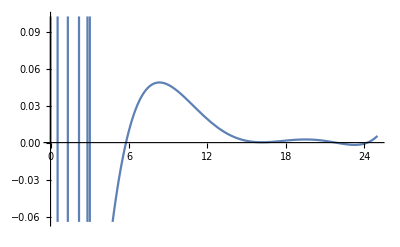

```mathematica
Plot[F5[x]/.{b->,c->,d->,e->,f->,g->,h->,i->,j->,k->,l->},{x,0,25}]
```

```mathematica
Plot[F5[x]/.{b->806.3561635287479,c->-2757.3877248298377,d->2968.0469808243215,e->-1258.9551767967641,f->183.40084016602486,g->-1.1527370808680644,h->0.44287540069649367,i->-0.0611674090738461,j->0.0039543260705112715,k->-0.00012195013163185386,l->1.4506338648209369*^-6},{x,5,25}]
```

```mathematica
Integrate[F5[x]/.{b->806.3561635287479,c->-2757.3877248298377,d->2968.0469808243215,e->-1258.9551767967641,f->183.40084016602486,g->-1.1527370808680644,h->0.44287540069649367,i->-0.0611674090738461,j->0.0039543260705112715,k->-0.00012195013163185386,l->1.4506338648209369*^-6},{x,0,25}]
```

12.9936

```mathematica
Plot[]
```